```mathematica
(* SIMULATION SCRIPT - Initialize populations parameters and data processing options *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
{Δc1,Δc2,U1,U2,popsize,starttime,timestep,maxtime}={0.01,0.01,1 10^-4,1 10^-4,10^6,0,1000,20000};
{verbose,veryverbose,fulldata,setseed}={False,False,0,7};
{windowsaddress,ubuntuaddress}={"C:/Users/dirge/Documents/kgrel2d/","~/Documents/kgrel2d/"};
rootaddress=ubuntuaddress;
workingfilename="_N-10p10_c1-0d01_c2-0d01_U1-1x10pn4_U2-1x10pn4_exp002.m";
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
```

```mathematica
(* SIMULATION SCRIPT - Print regime details, run simulation, and export data *)
(* ---------------------------------------------------------------------------------------------------------------------- *)(* ---------------------------------------------------------------------------------------------------------------------- *)
printRegimeDetails[Δc1,Δc2,U1,U2,popsize];
{genotypes,genotypeabundances}=getInitial2Ddistribution[5,popsize,Δc1,Δc2,U1,U2];
SeedRandom[setseed];
results=RunSimulationCheckEachMutation2[popsize,Δc1,Δc2,U1,U2,maxtime,timestep,genotypes,genotypeabundances];
Export[rootaddress<>"/data/simtest/simtest_data"<>ToString[fulldata]<>workingfilename<>".m",results];
Clear[results];
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
```

```mathematica
(* DATA ANALYSIS SCRIPT - Compute PDFs over relative fitness (computationally intensive ) *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
results=Import[rootaddress<>"data/simtest/simtest"<>workingfilename];
pdfvstime=ParallelTable[
temppdf=getMeanPDF[{results[[i]]}];
{results[[i]][[1]],temppdf[[1]],temppdf[[2]],results[[i]][[4]]},{i,1,Length[results]}];
Export[rootaddress<>"data/simtest/pdfvstime"<>workingfilename,pdfvstime];
Clear[results];
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
```

```mathematica
(* DATA ANALYSIS SCRIPT - Transform pdftime data to matrix data type and export *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
pdfvstime=Import[rootaddress<>"data/simtest/pdfvstime"<>workingfilename];
(* heatplot snapshot over various generations *)
traitbound=Max[Abs[Flatten[pdfvstime[[;;,2]]]]];
heatplotdata=ParallelTable[
heatdata=Array[0 #1 #2 &,{2traitbound+1,2traitbound+1}];
Do[heatdata[[traitbound+1-pdfvstime[[i]][[2]][[j]][[1]],pdfvstime[[i]][[2]][[j]][[2]]+traitbound+1]]=pdfvstime[[i]][[3]][[j]],{j,1,Length[pdfvstime[[i]][[2]]]}];
{pdfvstime[[i]][[1]],heatdata,pdfvstime[[i]][[4]]},{i,1,Length[pdfvstime]}];
Export[rootaddress<>"data/simtest/heatplotdata"<>workingfilename<>".m",heatplotdata];
Clear[pdfvstime,traitbound];
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
```

```mathematica
pdfvstime=Import[rootaddress<>"data/simtest/pdfvstime"<>workingfilename];
```

{{-0.707107,-4.94975},{-0.707107,-4.94975},{-2.12132,-4.94975},{0.707107,-4.94975},{-1.41421,-4.24264},{-2.82843,-4.24264},{0.,-4.24264},{-4.24264,-4.24264},{1.41421,-4.24264},{-0.707107,-3.53553},{-3.53553,-3.53553},{-2.12132,-3.53553},{0.707107,-3.53553},{2.12132,-3.53553},{1.41421,-2.82843},{-4.94975,-3.53553},{-1.41421,-2.82843},{-4.24264,-2.82843},{0.,-2.82843},{-2.82843,-2.82843},{-0.707107,-2.12132},{-7.77817,-3.53553},{2.82843,-2.82843},{0.,-1.41421},{3.53553,-2.12132},{2.12132,-2.12132},{-3.53553,-2.12132},{-5.65685,-2.82843},{-1.41421,-1.41421},{0.707107,-0.707107},{-4.94975,-2.12132},{-5.65685,-1.41421},{-4.24264,-1.41421},{4.24264,-1.41421},{-0.707107,-0.707107},{-2.82843,-1.41421},{-2.12132,-0.707107},{2.82843,-1.41421},{-4.94975,-0.707107},{0.,0.},{1.41421,0.},{-3.53553,-0.707107},{-1.41421,0.},{-6.36396,-0.707107},{-4.24264,0.},{4.94975,-0.707107},{-0.707107,0.707107},{-5.65685,0.},{3.53553,-0.707107},{-2.82843,0.},{0.707107,0.707107},{5.65685,0.},{4.24264,0.},{-3.53553,0.707107},{-2.12132,0.707107},{0.,1.41421},{2.12132,0.707107},{-4.94975,0.707107},{1.41421,1.41421},{-7.07107,0.},{-1.41421,1.41421},{-6.36396,0.707107},{-4.24264,1.41421},{0.707107,2.12132},{2.82843,1.41421},{4.94975,0.707107},{-0.707107,2.12132},{-7.77817,0.707107},{6.36396,0.707107},{-2.82843,1.41421},{2.12132,2.12132},{-7.07107,1.41421},{-5.65685,1.41421},{-2.12132,2.12132},{-3.53553,2.12132},{0.,2.82843},{1.41421,2.82843},{-4.94975,2.12132},{-1.41421,2.82843},{-7.77817,2.12132},{-2.82843,2.82843},{0.707107,3.53553},{-6.36396,2.12132},{-0.707107,3.53553},{3.53553,2.12132},{-5.65685,2.82843},{2.12132,3.53553},{-4.24264,2.82843},{-7.07107,2.82843},{5.65685,1.41421},{7.07107,1.41421},{-3.53553,3.53553},{-2.12132,3.53553},{0.,4.24264}}

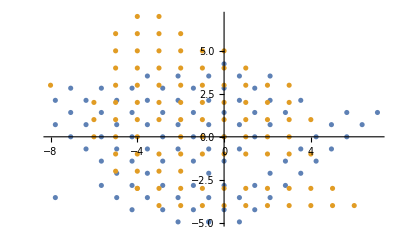

```mathematica
rotationmatrix={{Cos[Pi/4],-Sin[Pi/4]},{Sin[Pi/4],Cos[Pi/4]}};
rotatedfitnessclasses=(rotationmatrix.(pdfvstime[[1000]][[2]]ᵀ))ᵀ*1.0
ListPlot[{rotatedfitnessclasses,pdfvstime[[1000]][[2]]}]
```

```mathematica
{fitnessvariance1,fitnessvariance2}=(1/Total[pdfvstime[[1000]][[3]]])*({pdfvstime[[1000]][[3]]}.(rotatedfitnessclasses*rotatedfitnessclasses)-({pdfvstime[[1000]][[3]]}.rotatedfitnessclasses)^2)[[1]]
```

{0.652016,0.506638}

```mathematica
(* DATA ANALYSIS SCRIPT - Rotate data and compute expected normal (only valid for symmetric case) *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
pdfvstime=Import[rootaddress<>"data/simtest/pdfvstime"<>workingfilename];
rotationmatrix={{Cos[Pi/4],-Sin[Pi/4]},{Sin[Pi/4],Cos[Pi/4]}};
(* heatplot snapshot over various generations *)
rotatedpdfvstime=ParallelTable[
rotatedfitnessclasses=(rotationmatrix.(pdfvstime[[i]][[2]]ᵀ))ᵀ;
{rvar1,rvar2}=(1/Total[pdfvstime[[i]][[3]]])*({pdfvstime[[i]][[3]]}.(rotatedfitnessclasses*rotatedfitnessclasses)-({pdfvstime[[i]][[3]]}.rotatedfitnessclasses)^2)[[1]];
expectedfrequencies=Table[1/(2 π √(rvar1 rvar2))Exp[-1/2((rotatedfitenssclasses[[i]][[1]])^2/rvar1+(rotatedfitnessclasses[[i]][[2]])^2/rvar2)],{i,1,Length[rotatedfitnessclasses]}]
covariancematrix=rotationmatrix.Diagonal[{rvar1,rvar2}].(rotationmatrixᵀ);
{pdfvstime[[i]][[1]],rotatedfitnessclasses,expectedfrequencies,pdfvstime[[i]][[4]],covariancematrix},{i,1,Length[pdfvstime]}];
Export[rootaddress<>"data/simtest/rotatedpdfvstime"<>workingfilename,heatplotdata];
Clear[pdfvstime,rotationmatrix,rotatedpdf];
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
```

```mathematica
(* PLOT SCRIPT - Create Plots with matrix data *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
heatplotdata=Import[rootaddress<>"data/simtest/heatplotdata"<>workingfilename<>".m"];
offset=2000;
ParallelDo[
Export[rootaddress<>"plots/simplots1/short/heatplot"<>workingfilename<>ToString[i]<>".jpg",MatrixPlot[Log10[heatplotdata[[i+offset]][[2]]],PlotLabel->"t="<>ToString[heatplotdata[[i+offset]][[1]]]<>", mean="<>ToString[(heatplotdata[[i+offset]][[3]]-{1,1})*{Δc1^-1,Δc2^-1}],PlotLegends->Automatic]]
,{i,1,100}];
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
```

```mathematica
(* PLOT SCRIPT - Export plots of symmetric evolution - requires data0 type *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
results=Import[rootaddress<>"data/simtest/summarydata"<>workingfilename];
Export[rootaddress<>"plots/timevsload"<>StringDrop[workingfilename,-2]<>".gif",
ListPlot[results[[;;,{1,9}]],AxesLabel->{"Time","Substitutional Load"},PlotLabel->"Substitutional Load vs Time: mean load = "<>ToString[Mean[Table[results[[i]][[9]],{i,1,Length[results]}]]]]];
Export[rootaddress<>"plots/timevsmeans"<>StringDrop[workingfilename,-2]<>".gif",
ListPlot[{results[[;;,{1,2}]],results[[;;,{1,3}]]},PlotStyle->{Blue,Red},PlotLegends->{"mean trait 1","mean trait 2"},AxesLabel->{"Time","mean fitness"},PlotLabel->"mean fitness vs Time"]];
Export[rootaddress<>"plots/timevsvariances"<>StringDrop[workingfilename,-2]<>".gif",
ListPlot[{results[[;;,{1,6}]],results[[;;,{1,7}]],results[[;;,{1,5}]]},PlotStyle->{Blue,Red,Black},PlotLegends->{"variance trait 1","variance trait 2","covariance"},AxesLabel->{"Time","Variances"},PlotLabel->"Variances vs Time"]];
Export[rootaddress<>"plots/timevscovariance"<>StringDrop[workingfilename,-2]<>".gif",
ListPlot[{results[[;;,{1,5}]]},PlotStyle->{Black},PlotLegends->{"variance trait 1","variance trait 2","covariance"},AxesLabel->{"Time","Variances"},PlotLabel->"mean covariance " <>ToString[Mean[results[[;;,{5}]]]]]];
Clear[results];
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
```